```mathematica
SetDirectory["/home/bjorn/Documents/CU/PHYS_4430"]
```

/home/bjorn/Documents/CU/PHYS_4430

```mathematica
data=Import["/home/bjorn/Documents/CU/PHYS_4430/gauss_width_milli.csv"]
```

{{Position (mm),Power in (mW)},{6.985,5.69536},{7.0104,5.69536},{7.0358,5.69536},{7.0612,5.66383},{7.0866,5.64806},{7.112,5.64806},{7.1374,5.63229},{7.1628,5.61652},{7.1882,5.58499},{7.2136,5.56922},{7.239,5.53769},{7.2644,5.50615},{7.2898,5.45885},{7.3152,5.41154},{7.3406,5.3327},{7.366,5.26963},{7.3914,5.17502},{7.4168,5.06465},{7.4422,4.92274},{7.4676,4.74929},{7.493,4.57584},{7.5184,4.37086},{7.5438,4.10281},{7.5692,3.86629},{7.5946,3.614},{7.62,3.33018},{7.6454,3.09366},{7.6708,2.7783},{7.6962,2.51025},{7.7216,2.25796},{7.747,2.02144},{7.7724,1.78493},{7.7978,1.53895},{7.8232,1.3245},{7.8486,1.11006},{7.874,0.946074},{7.8994,0.794702},{7.9248,0.655944},{7.9502,0.529801},{7.9756,0.441501},{8.001,0.340587},{8.0264,0.277515},{8.0518,0.227058},{8.0772,0.1766},{8.1026,0.138757},{8.128,0.100915},{8.1534,0.0756859},{8.1788,0.0504573},{8.2042,0.0425733},{8.2296,0.0331126},{8.255,0.029959},{8.2804,0.0204983},{8.3058,0.0141911},{8.3312,0.0126143},{8.3566,0.0110375},{8.382,0.00946074},{8.4074,0.00788395},{8.4328,0.00473037},{8.4582,0.00315358},{8.4836,0.00315358},{8.509,0.00157679},{8.5344,0.00157679},{8.5598,0.00157679},{8.5852,0.00157679}}

```mathematica
data1=data[[2;;]];
```

```mathematica
fit = NonlinearModelFit[data1,a*Erfc[b*x+c]+d,{a,b,c,d},x]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[1.+1. Erfc[1.+1. x]]

General::unfl: Underflow occurred in computation.

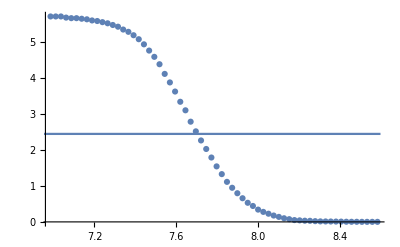

```mathematica
Show[ListPlot[data1],Plot[fit[x],{x,6.8,8.6}]]
```

```mathematica
data1*10^-3
```

{{0.006985,0.00569536},{0.0070104,0.00569536},{0.0070358,0.00569536},{0.0070612,0.00566383},{0.0070866,0.00564806},{0.007112,0.00564806},{0.0071374,0.00563229},{0.0071628,0.00561652},{0.0071882,0.00558499},{0.0072136,0.00556922},{0.007239,0.00553769},{0.0072644,0.00550615},{0.0072898,0.00545885},{0.0073152,0.00541154},{0.0073406,0.0053327},{0.007366,0.00526963},{0.0073914,0.00517502},{0.0074168,0.00506465},{0.0074422,0.00492274},{0.0074676,0.00474929},{0.007493,0.00457584},{0.0075184,0.00437086},{0.0075438,0.00410281},{0.0075692,0.00386629},{0.0075946,0.003614},{0.00762,0.00333018},{0.0076454,0.00309366},{0.0076708,0.0027783},{0.0076962,0.00251025},{0.0077216,0.00225796},{0.007747,0.00202144},{0.0077724,0.00178493},{0.0077978,0.00153895},{0.0078232,0.0013245},{0.0078486,0.00111006},{0.007874,0.000946074},{0.0078994,0.000794702},{0.0079248,0.000655944},{0.0079502,0.000529801},{0.0079756,0.000441501},{0.008001,0.000340587},{0.0080264,0.000277515},{0.0080518,0.000227058},{0.0080772,0.0001766},{0.0081026,0.000138757},{0.008128,0.000100915},{0.0081534,0.0000756859},{0.0081788,0.0000504573},{0.0082042,0.0000425733},{0.0082296,0.0000331126},{0.008255,0.000029959},{0.0082804,0.0000204983},{0.0083058,0.0000141911},{0.0083312,0.0000126143},{0.0083566,0.0000110375},{0.008382,9.46074×10^-6},{0.0084074,7.88395×10^-6},{0.0084328,4.73037×10^-6},{0.0084582,3.15358×10^-6},{0.0084836,3.15358×10^-6},{0.008509,1.57679×10^-6},{0.0085344,1.57679×10^-6},{0.0085598,1.57679×10^-6},{0.0085852,1.57679×10^-6}}

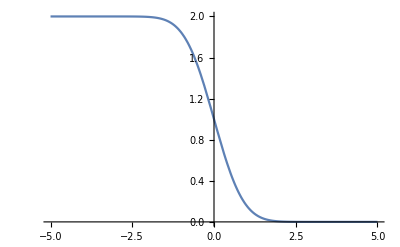

```mathematica
Plot[Erfc[x],{x,-5,5}]
```

```mathematica
test=NonlinearModelFit[data1*10^-3,a*Erfc[b*x+c]+d+e*x,{a,b,c,d},{{a,.0057},{c,.0077}},x]
```

NonlinearModelFit::nonopt: Options expected (instead of x) beyond position 4 in «1». An option must be a rule or a list of rules.

NonlinearModelFit[{{0.006985,0.00569536},{0.0070104,0.00569536},{0.0070358,0.00569536},{0.0070612,0.00566383},{0.0070866,0.00564806},{0.007112,0.00564806},{0.0071374,0.00563229},{0.0071628,0.00561652},{0.0071882,0.00558499},{0.0072136,0.00556922},{0.007239,0.00553769},{0.0072644,0.00550615},{0.0072898,0.00545885},{0.0073152,0.00541154},{0.0073406,0.0053327},{0.007366,0.00526963},{0.0073914,0.00517502},{0.0074168,0.00506465},{0.0074422,0.00492274},{0.0074676,0.00474929},{0.007493,0.00457584},{0.0075184,0.00437086},{0.0075438,0.00410281},{0.0075692,0.00386629},{0.0075946,0.003614},{0.00762,0.00333018},{0.0076454,0.00309366},{0.0076708,0.0027783},{0.0076962,0.00251025},{0.0077216,0.00225796},{0.007747,0.00202144},{0.0077724,0.00178493},{0.0077978,0.00153895},{0.0078232,0.0013245},{0.0078486,0.00111006},{0.007874,0.000946074},{0.0078994,0.000794702},{0.0079248,0.000655944},{0.0079502,0.000529801},{0.0079756,0.000441501},{0.008001,0.000340587},{0.0080264,0.000277515},{0.0080518,0.000227058},{0.0080772,0.0001766},{0.0081026,0.000138757},{0.008128,0.000100915},{0.0081534,0.0000756859},{0.0081788,0.0000504573},{0.0082042,0.0000425733},{0.0082296,0.0000331126},{0.008255,0.000029959},{0.0082804,0.0000204983},{0.0083058,0.0000141911},{0.0083312,0.0000126143},{0.0083566,0.0000110375},{0.008382,9.46074×10^-6},{0.0084074,7.88395×10^-6},{0.0084328,4.73037×10^-6},{0.0084582,3.15358×10^-6},{0.0084836,3.15358×10^-6},{0.008509,1.57679×10^-6},{0.0085344,1.57679×10^-6},{0.0085598,1.57679×10^-6},{0.0085852,1.57679×10^-6}},d+e x+a Erfc[c+b x],{a,b,c,d},{{a,0.0057},{c,0.0077}},x]

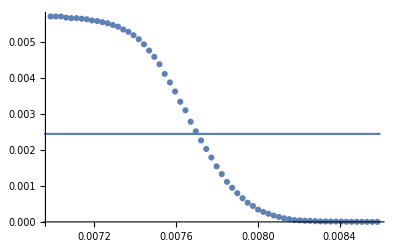

```mathematica
Show[ListPlot[data1*10^-3],Plot[test[x],{x,0.0068,0.0086}]]
```